```mathematica
Series[1/x ArcSin[√x]^2,{x,0,4}]
```

1+x/3+(8 x^2)/45+(4 x^3)/35+(128 x^4)/1575+O[x]^(9/2)

```mathematica
Series[(-2 M^2)-2/m^2 ArcSin[√(1/rho)]^2/.{rho-> 4 M^2/m^2},{m,0,4}]
```

1+m^2/(12 M^2)+m^4/(90 M^4)+O[m]^5

```mathematica
Series[1/x 3/2 1/(2 M)(2M + M(4 M^2 - m^2)(-2/m^2)ArcSin[m/(2 M)]^2)/.{m->2 √x M},{x,0,3}]
```

1+(7 x)/30+(2 x^2)/21+(26 x^3)/525+O[x]^(7/2)

```mathematica
%/(x^2/6)
```

6/x^2+7/(5 x)+4/7+(52 x)/175+O[x]^(3/2)

### From hep - ph/9603205 (Appendix A1): x = (m_S/(2 m_Q))^2

```mathematica
fLight[x_]=3/2 Normal[Series[z(1+(1-z)ArcSin[1/(√z)]^2)/.{z->1/x},{x,0,8}]];
fHeavy[x_]=FullSimplify[3/2 Normal[Series[z(1+(1-z)(-1/4(Log[-(1+√(1-z))/(1-√(1-z))])^2)),{z,0,8}]]/.{z->1/x},Assumptions->{x>1}];
fLight2[x_]:=3/2(z(1+(1-z)ArcSin[1/(√z)]^2))/.{z->1/x};
fHeavy2[x_]:=(3/2(z(1+(1-z)(-1/4(Log[-(1+√(1-z))/(1-√(1-z))])^2)))/.{z->1/x});
fAll[x_]=If[x<1,fLight[x],fHeavy[x]];
fAll2[x_]:=If[x<1,fLight2[x],fHeavy2[x]];
```

```mathematica
FullSimplify[fLight2[x],Assumptions->{x>0}]
```

(3 (x+(-1+x) ArcSin[√x]^2))/(2 x^2)

```mathematica
FullSimplify[fHeavy2[x],Assumptions->{x>0}]
```

(12 x-3 (-1+x) Log[1-2 x-2 √((-1+x) x)]^2)/(8 x^2)

```mathematica
fAll2[0.1]
fLight[0.1]
```

1.02434

1.02434

```mathematica
Expand[fLight[x]]
Expand[fHeavy[x]]
```

1+(7 x)/30+(2 x^2)/21+(26 x^3)/525+(512 x^4)/17325+(1216 x^5)/63063+(128 x^6)/9555+(640 x^7)/65637+(229376 x^8)/31177575

71/(12288 x^8)+4003/(491520 x^7)+49/(4096 x^6)+37/(2048 x^5)+3/(128 x^4)-3/(32 x^3)+3/(2 x)-(165 Log[-4 x])/(28672 x^8)-(357 Log[-4 x])/(40960 x^7)-(147 Log[-4 x])/(10240 x^6)-(55 Log[-4 x])/(2048 x^5)-Log[-4 x]/(16 x^4)-(15 Log[-4 x])/(64 x^3)+(3 Log[-4 x])/(8 x^2)+(3 Log[-4 x]^2)/(8 x^2)-(3 Log[-4 x]^2)/(8 x)

```mathematica
fHeavy[1.]
```

1.50475+0.0705083 ⅈ

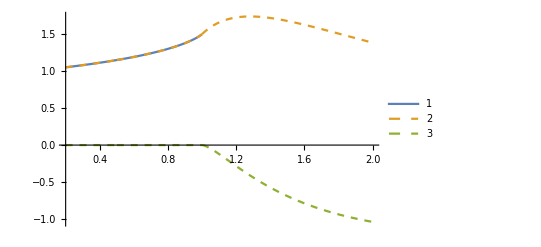

```mathematica
Plot[{fLight2[x],Re[fHeavy2[x]],Im[fHeavy2[x]]},{x,0.2,2},PlotLegends->Automatic,PlotStyle->{Thick,Dashed,Dashed}]
```

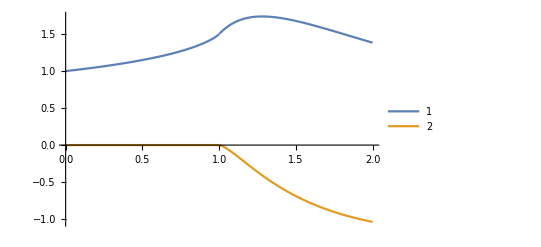

```mathematica
Plot[{Re[fAll2[x]],Im[fAll2[x]]},{x,0.,2},PlotLegends->Automatic]
```

```mathematica
fAll2[x]
```

If[x<1,fLight2[x],fHeavy2[x]]

```mathematica
Expand[FullSimplify[fLight2[1/z]]]
```

(3 z)/2+3/2 z ArcCsc[√z]^2-3/2 z^2 ArcCsc[√z]^2

```mathematica
InputForm[%]
```

(3*z)/2 + (3*z*ArcCsc[Sqrt[z]]^2)/2 - (3*z^2*ArcCsc[Sqrt[z]]^2)/2

```mathematica
Expand[FullSimplify[fHeavy2[1/z],Assumptions->{z>0}]]
InputForm[%]
```

(3 z)/2-3/8 z Log[1-(2 (1+√(1-z)))/z]^2+3/8 z^2 Log[1-(2 (1+√(1-z)))/z]^2

(3*z)/2 - (3*z*Log[1 - (2*(1 + Sqrt[1 - z]))/z]^2)/8 + (3*z^2*Log[1 - (2*(1 + Sqrt[1 - z]))/z]^2)/8

```mathematica
Expand[FullSimplify[fHeavy2[1/z]]]/.{z->0}
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ∞ encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ∞ encountered.

Indeterminate